# Physics 230 -- Lab 13 (Optimization)

## Branton J. Campbell, BYU Physics & Astronomy, Winter 2010 R. Steven Turley, BYU Physics and Astronomy, Fall 2011

"Optimization" refers to the process of adjusting the free parameters of a complicated system until it achieves some kind of optimal property or behavior.  Optimization methods, in addition to being relevant to all fields of scientific and technical study, are an important field of research in their own right.  In this lab, we will become familiar with some of Mathematica's optimization "tools" and the well-known optimization "algorithms" that they use.  We will also explore two of the most well-known optimization problems: finding the extrema of smooth single-variable functions and fitting model functions to experimental data.  The "Mathematics and Algorithms" section of the DC home page has a link to the Optimization guide page, which provides quick-reference to numerous related optimization functions and tutorials.  The Wikipedia has some nice information on optimization algorithms.

## Finding extrema (50 min)

Mathematica provides a number of tools for finding extrema.  FindMinimum (also see FindMaximum) searches numerically for a local minimum beginning at a user-specified starting point.  NMinimize (also see NMaximize) searches numerically for a global minimum.  Minimize (also see Maximize) can perform an analytical search for minima, though it defaults to NMinimize if given numeric input.

Each of these tools can perform either constrained or unconstrained optimizations of single-variable and multi-variable functions.  An unconstrained optimization is one in which there are no limitations on the parameters being fit.  In a constrained optimization, you tell Mathematica to enforce conditions on the data.  For example, let’s say you were fitting a function the steady state temperature in a conducting slab connecting two reservours at different temperatures.  You would expect that the temperature anywhere in the slab would be between the temperatures of the two reservoirs at either end.  Therefore, a reasonable constraint on the optimization would be that the temperature lie in this range.

Countless optimization algorithms have been developed over time.  A handful of well-known algorithms are available within Mathematica.  These algorithms each differ from one another in the way that they sample the function being optimized.  Some algorithms choose sample points randomly, while others take well-defined steps that depend on the local shape of the function and/or a limited number of previous sample points.  Some algorithms extract random steps from a statistical distribution and/or use a probability relation to decide whether or not to accept a computed step.  Some of the more sophisticated algorithms use concepts from biological diversity to explore complicated parameter spaces -- we call them "evolutionary" algorithms.  One of the simplest algorithms simply rolls downhill until it finds the nearest minimum.  In the following exercises, we will attempt to visualize the inner workings of Mathematica's minimization tools and algorithms in order to develop some intuition regarding their use.

### (#1) Introduction (15 min)

(a) Evaluate the cell below to define a single-variable function, multimin[x_], which has several local minima, but only one global minimum.  We plot this function together with its first and second derivatives.  How many minima do you see?  Use these plots to demonstrate for your TA that minima are located at positions where the first derivative crosses zero and where the second derivative is positive.

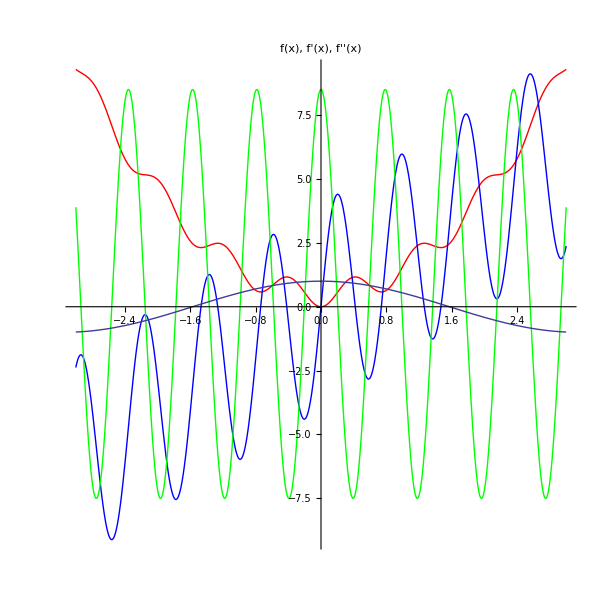

```mathematica
multimin[x_] := x^2+Sin[4*x]^2
p0 = Plot[multimin[x],{x,-3,3}, PlotRange->All,PlotStyle->{Thick,Red}];
p1 = Plot[multimin'[x],{x,-3,3}, PlotRange->All,PlotStyle->{Thick,Blue}];
p2 = Plot[multimin''[x]/4,{x,-3,3}, PlotRange->All,PlotStyle->{Thick,Green}];
Show[{p0,p1,p2,p3},AspectRatio->1,ImageSize->600,PlotLabel->Style["f(x), f'(x), f''(x)",Large]]
```

(b) Use FindMinimum to locate a local minimum of multimin, starting with x_0=1.0 as a starting point.  On a separate line, use variable replacement to extract a numerical value for the x-axis location of the minimum.  Explain the format of the the FindMinimum output to your TA.

```mathematica
min1b =FindMinimum[multimin[x],{x,1}]
```

{0.58016,{x→0.738147}}

```mathematica
x/.min1b[[2]]
```

0.738147

(c) Use NMinimize to find the global minimum of of multimin.  If you obtain a very small result that closely approximates zero, use postfix notation to Chop the result to the nearest millionth.

```mathematica
NMinimize[multimin[x],x]//Chop
```

{0,{x→0}}

(d) Use NMinimize to find the global minimum of of multimin, constrained by the condition x < -1.2.  If you obtain a very small result that closely approximates zero, use postfix notation to Chop the result to the nearest millionth.  Explain this result to your TA.

```mathematica
NMinimize[{multimin[x],x<-1.2},x]//Chop
```

{2.31478,{x→-1.46779}}

(e) Use NMinimize to find the global minimum of of multimin, constrained by the condition x > 2.  If you obtain a very small result that closely approximates zero, use postfix notation to Chop the result to the nearest millionth.  Explain this result to your TA.

```mathematica
NMinimize[{multimin[x],x>2},x]//Chop
```

{4.97883,{x→2.}}

### (#2) Unconstrained vs constrained local minimization (10 min)

(a) The function multimin the cell below was expanded from the previous exercise into two dimensions.  Try each of the local methods available for unconstrained optimizations (i.e. “ConjugateGradient”, “PrincipalAxis”, “LevenbergMarquardt”,”Newton”,”QuasiNewton”, and ”InteriorPoint”) and compared the answers they give and the number of iterations required.  Start each minimization at the point x=3, y=-3.  I have given an example of how to do this with the default Automatic method.  If a run seems to be taking way too long, abort it (memorize the Alt-. keyboard shortcut) and shorten the delay.

```mathematica
multimin2[x_,y_] := x^2+y^2+2*Sin[4*x]^2+1.5*Cos[3*y]^2
Plot3D[multimin2[x,y],{x,-4,4},{y,-4,3}]
calls=0;
val=FindMinimum[multimin2[x,y],{x,3}, {y,-3},EvaluationMonitor:>calls++];
StringForm["`` method required `` calls and returned a minimum of `` at ``", method, calls, NumberForm[val[[1]],3], val[[2]]]
```

-Graphics3D-

method method required 12 calls and returned a minimum of "11.8" at {x → 3.03397, y → -1.45372}

(b) Repeat this test with the Automatic method "Constrained" by the requirement that 2<x<3 and -1 < y < 0.  Use the x=2.4 and y=-0.5 as an initial guess. The optimization should converge fairly quickly.  Compare your constrained result to that of the unconstrained optimization above.

```mathematica
myval=FindMinimum[{multimin2[x,y],2<x<3,-1<y<0},{x,3}, {y,-3},EvaluationMonitor:>calls++];
StringForm["`` method required `` calls and returned a minimum of `` at ``", method, calls, NumberForm[myval[[1]],3], myval[[2]]]
```

method method required 22 calls and returned a minimum of "5.63" at {x → 2.28037, y → -0.48722}

(c) Try again starting at the point x=2.4, y=-0.3 and notice the result.  Discuss the message you get with your TA.

```mathematica
myval2=FindMinimum[{multimin2[x,y],2<x<3,-1<y<0},{x,2.4}, {y,-0.3},EvaluationMonitor:>calls++];
StringForm["`` method required `` calls and returned a minimum of `` at ``", method, calls, NumberForm[myval2[[1]],3], myval2[[2]]]
```

method method required 31 calls and returned a minimum of "5.63" at {x → 2.28037, y → -0.48722}

### (#3) Global minimization (5 min)

Repeat the previous exercise looking for a global minimum rather than a local minimum.  Count the number of calls as before and discuss any difference you see with your TA.

```mathematica
numcall =0;
abmin =NMinimize[{multimin2[x,y],2<x<3,-1<y<0},{x,y},EvaluationMonitor:>numcall++];
StringForm["`` method required `` calls and returned a minimum of `` at ``", method, calls, NumberForm[abmin[[1]],3], abmin[[2]]]

numcall =0;
abmin2 =NMinimize[{multimin2[x,y],2<x<3,-1<y<0},{x,y},EvaluationMonitor:>numcall++];
StringForm["`` method required `` calls and returned a minimum of `` at ``", method, calls, NumberForm[abmin2[[1]],3], abmin2[[2]]]
```

method method required 31 calls and returned a minimum of "5.63" at {x → 2.28037, y → -0.48722}

method method required 31 calls and returned a minimum of "5.63" at {x → 2.28037, y → -0.48722}

### (#4) Analytical and symbolic optimization (10 min)

(a) In the cell below, attempt to use Minimize to find the analytical global mininum of multimin(x).  You will find that Minimize struggles with all but the simplest trancendental equations, though it works quite reliably on polynomials.

```mathematica
multimin[x_] := x^2+Sin[4*x]^2
```

```mathematica
Minimize[multimin[x],x]
```

{0,{x→0}}

(b) Evaluate the cell below to define a quartic-polynomial function, doublemin(x), which has one local minimum and one global minimum.  Use Minimize (or Maximize) to perform the following tasks:  (1) Find the global minimum.  (2) Find the global minimum subject to the constraint x > 0.  (3) Find the global minimum subject to the constraint -1 < x < 1.  (4) Find the global maximum.  (5) Find the global maximum subject to the constraint -1 < x < 1.

```mathematica
doublemin[x_] :=(3 x^4-x^3-24 x^2+12x+12)/24
Minimize[doublemin[x],x]
Minimize[{doublemin[x],x>0},x]
Minimize[{doublemin[x],-1<x<1},x]
Maximize[{doublemin[x]},x]
Maximize[{doublemin[x],-1<x<1},z]
```

{-13/6,{x→-2}}

{-5/6,{x→2}}

Minimize::wksol: Warning: There is no minimum in the region in which the objective function is defined and the constraints are satisfied; returning a result on the boundary.

{-5/6,{x→-1}}

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{∞,{x→-∞}}

{Piecewise[{{1/24 (12+12 x-24 x^2-x^3+3 x^4), -1<x<1}, {-∞, True}}],{z→Piecewise[{{0, -1<x<1}, {Indeterminate, True}}]}}

(c)  Minimize a x^2+b x+c, where a, b and c are undefined constants.  Study the three logical/symbolic solutions and explain the output to your TA.  Which of the three solutions corresponds to the case where {a → 1, b → -2, c → 1}?  On a separate line, use variable substitution to see what the solution looks like in this special case.  Does it agree with the previous logical/symbolic expression?

```mathematica
Minimize[a*x^2+b*x+c,x]
```

{Piecewise[{{c, (b==0&&a==0)||(b==0&&a>0)}, {(-b^2+4 a c)/(4 a), (b>0&&a>0)||(b<0&&a>0)}, {-∞, True}}],{x→Piecewise[{{0, (b==0&&a==0)||(b==0&&a>0)}, {-b/(2 a), (b>0&&a>0)||(b<0&&a>0)}, {Indeterminate, True}}]}}

## Curve fitting (45 min)

"Curve fitting" refers to the process of finding the function that best matches a set of data points.  The word "curve", however, doesn't restrict us to one dimension -- it could also refer to multidimensional surfaces in higher-dimensional spaces.  To fit a curve, we needs four things: (1) a discrete set of numerical data, (2) a "model" (i.e. the function that we plan to fit to our data) with adjustable "fitting parameters", (3) a "cost" function (also called an "energy" function or an "objective" function) that quantifies how bad our fit is, and (4) an algorithm for minimizing our cost function.  If we think of the fitting parameters the components of a "vector" or "sample point" in "model space", our algorithm should move the sample point around in model space until it finds the point where the cost is minimized.  And if we choose and implement our algorithm carefully, it will find the best global fit to our data rather than getting stuck in a local minimum.

### (#5) Linear curve fitting (10 min)

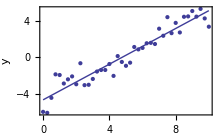
It is always possible to find a linear model of the form m x+b that optimally fits an xy dataset.  In other words, we can find the coefficients m and b that send a straight line right though the data with minimal discrepancies.  Linear fitting problems have well-defined analytic solutions that are trivially easy to compute.  Mathematica won't break a sweat.

-Graphics-

If we define an linear function, f(x) = m x + b, we can determine the values m and b that best fit the data by defining and minimizing a cost function that measures the "badness of fit".  The most common measure is the sum of the squares of individual data-model discrepancies,  cost = ∑ _n (y_n-f(x_n))^2.  For obvious reasons, we call this a "least squares" cost function.  The optimal values of m and b will be those that minimize the squared model-data discrepancies.

The least squares criterion has an important statistical basis when used to fit measured data.  It is an example of a “maximum likelihood” method for finding a fit.  If we assume that the noise in the data is due to a process with a normal distribution (which is very often the case), then the probability of measuring a value of y_n  when the “true” value is f(x_n) is (exp(-(y_n-f(x_n))^2/(2 σ_n^2)))/(√(2 π) σ_n).   The probability of measuring all of the  y_n points is the product of the individual probabilities. P=∏_(n=1)^N exp(-(y_n-f(x_n))^2/(2 σ_n^2)).  A product of exponentials is equal to the exponential of the sum of the arguments.
P=exp(-∑_(n=1)^N (y_n-f (x_n))^2/(2 σ_n^2))
We want to find the distribution which is the most likely one to have generated our measured values.  In other words, we want to find the function f which maximizes P.  Since the exponential function with a negative argument is monotonically decreasing, this function will be the one which minimizes ∑_(n=1)^N (y_n-f(x_n))^2/σ_n^2.  A simple least squares fit is one under that assumption that all of the σ_n  have equal values.  A weighted least squares fit allows for the possibilities that the σ_n might be different.

(a) Import and plot the data in the file linearData.xls.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/GrantLyon/Desktop

```mathematica
lindata = Import["linearData.xls"][[1]]
```

{{0.,10.4609},{0.25,9.80207},{0.5,7.47375},{0.75,9.13083},{1.,10.7404},{1.25,8.48726},{1.5,7.60549},{1.75,7.29843},{2.,9.80043},{2.25,7.41271},{2.5,8.38187},{2.75,5.96955},{3.,6.27509},{3.25,7.79094},{3.5,5.94783},{3.75,4.50567},{4.,8.26998},{4.25,4.73415},{4.5,5.64545},{4.75,5.21304},{5.,4.26846},{5.25,5.24689},{5.5,5.35737},{5.75,4.40203},{6.,4.82737},{6.25,3.6386},{6.5,2.90188},{6.75,2.75608},{7.,2.96602},{7.25,2.68964},{7.5,3.46872},{7.75,2.46414},{8.,2.03379},{8.25,1.16079},{8.5,0.0698906},{8.75,0.269668},{9.,1.47669},{9.25,-1.04956},{9.5,-0.422598},{9.75,1.28018},{10.,0.584434}}

(c) Use Fit to perform a linear fit to the xy data read in above.  In other words, find the function y=mx+b which best fits the data.  Plot the data and the fit on the same graph.

9.98847-1.01557 x

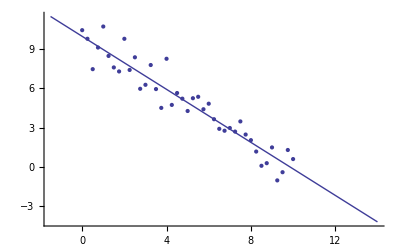

```mathematica
fitfunc = Fit[lindata,{1,x},x]
dp = ListPlot[lindata];
fp = Plot[fitfunc,{x,-1.5,14}];
Show[dp,fp]
```

### (#6) Fitting linear-combinations of arbitrary functions (10 min)

(a) Read in the x,y data in the file nonlinearData.xls and plot it using ListPointPlot3D.

```mathematica
nonlindata = Import["nonlinearData.xls"][[1]];
```

```mathematica
ListPlot3D[nonlindata]
```

-Graphics3D-

(b) Fit the data to a function of the form z(x,y)=a+b x+c x^2 y^2+d 0y.  The function J_0()y is the Mathematica function BesselJ[0,y].  Notice that while z(x,y) is non-linear overall, it can still be viewed as a linear combination of four functions with variable coefficients.  Because this is the case, finding the coefficients that best fit the data can still be treated as a linear (and analytically solvable) problem.  Thus, while Mathematica’s Fit function can ONLY be used for linear fitting problems, we can apply it here.  Explain this to your TA. ListPointPlot3D the data and Plot3D the resulting fit on the same graph.

```mathematica
funcfit = Fit[nonlindata,{1,x,x^2*y^2,BesselJ[0,y]},{x,y}]
Show[ListPointPlot3D[nonlindata,PlotStyle->Red],Plot3D[funcfit,{x,-10,10},{y,-10,10},PlotStyle->Black]]
```

-2.57951+0.170958 x+0.000746787 x^2 y^2+3.18055 BesselJ[0,y]

-Graphics3D-

### (#7) Nonlinear least-squares (NLSQ) fitting (15 min)

Most curve-fitting applications that you will encounter in practice will be nonlinear.  It is very important to appreciate that nonlinear fits do not generally have analytical solutions, but must be solved, instead, by iterative global cost-minimization.  Recall how problematic this was in the global minimization exercises above.

(a) Import the data in the file nonlinearData.dat.  Plot this data together with a nonlinear exponential-decay model of the form y=a exp(-x/b)+c.  Manually adjust the fitting parameters, (a, b and c), until the model appears to optimially fit the data.  You are essentially implementing a visual minimization algorithm in your head.  Show the result to your TA and discuss how you found the parameters a, b and c.

```mathematica
nonlindat = Import["nonlinearData.dat"]
Manipulate[Show[ListPlot[nonlindat],Plot[a*Exp[-x/b]+c,{x,-1,10}]],{{a,5},-5,15},{{b,4.44},-5,10},{{c,2.92},-5,5}]
```

Import::nffil: File not found during Import.

$Failed

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ListPlot[$Failed], GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[27]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 3.4000000000000004`]], Rule[PlotRange, List[List[-1, 10], List[3.4458105568181283`, 9.183023696451578`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]].

ListPlot::lpn: nonlindat is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ListPlot[nonlindat], GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[27]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 3.4000000000000004`]], Rule[PlotRange, List[List[-1, 10], List[3.4458105568181283`, 9.183023696451578`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]].

ListPlot::lpn: TraditionalForm`nonlindat is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in TraditionalForm`.

(b) Use Mathematica's built-in FindFit function to repeat the nonlinear least-squares fit that you performed manually above.  How do the results compare to your manual fit?

```mathematica
FindFit[nonlindat,a*Exp[-x/b]+c,{a,b,c},x]
```

{a→14.0959,b→3.88105,c→2.60481}

### (#8) Fitting uncertainties (10 min)

When you fit data, your data is probably subject to some random errors, and therefore possesses some statistical uncertainty.  After performing a fit, you will generally want to compute the statistical uncertainty in the value of each fitting parameter.  If you replace Fit with LinearModelFit FindFit with NonlinearModelFit you can find these uncertainties (and many other properties of your fits.

(a) The file nonlinearError.dat has a similar xy dataset used for an earlier nonlinear least-squares fitting exercisebut with a third column of data that contains the experimental uncertainties in the measured y values.  Read in and plot this data with the included error bars using the function ErrorBarListPlot defined below.  This function takes a list of {x,y,uncertainty} values and plots them with an associated error bar.  You can use the same PlotOptions as you can with ListPlot.  For example, you probaly want to set the PlotRange to {0,16}.

(1 | 13.8425 | 1.31387
2 | 10.5968 | 1.18028
3 | 8.7823 | 1.08637
4 | 7.58313 | 1.01296
5 | 6.79541 | 0.95812
6 | 6.11933 | 0.90573
7 | 4.97807 | 0.80252
8 | 4.07347 | 0.70225
9 | 4.18155 | 0.71534
10 | 3.5588 | 0.63471
11 | 3.36735 | 0.60706
12 | 3.08605 | 0.56345
13 | 3.31048 | 0.59855
14 | 3.10261 | 0.56612
15 | 2.35429 | 0.42812
16 | 2.9631 | 0.54312
17 | 2.89468 | 0.53144
18 | 2.35118 | 0.42746
19 | 2.65534 | 0.48829
20 | 2.74187 | 0.50432
21 | 2.91863 | 0.53556
22 | 2.70865 | 0.49823
23 | 3.04143 | 0.55616
24 | 2.8579 | 0.52504
25 | 2.73896 | 0.50379
26 | 2.99886 | 0.54912
27 | 2.75556 | 0.50681
28 | 2.36882 | 0.4312
29 | 2.58676 | 0.4752
30 | 2.20919 | 0.39631
31 | 2.17119 | 0.38764)

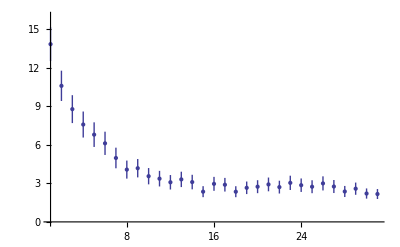

```mathematica
Needs["ErrorBarPlots`"]
ErrorBarListPlot[list_,opts:OptionsPattern[]]:=ErrorListPlot[{{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&/@list, FilterRules[{opts}, Options[ErrorListPlot]]]
nonlinerr = Import["nonlinearError.dat"]
ErrorBarListPlot[nonlinerr,PlotRange->{0,16}]
```

(b) Fit this data to the same exponential decay law as in the previouis example using NonlinearModelFit with Weights → 1/uncertainty^2 as an option.  Name the resulting nonlinear FittedModel nlm.

```mathematica
{xs,ys,uncertainties} = Transpose[nonlinerr];
nlmdata = Transpose[{xs,ys}]//StandardForm
```

{{1,13.8425},{2,10.5968},{3,8.7823},{4,7.58313},{5,6.79541},{6,6.11933},{7,4.97807},{8,4.07347},{9,4.18155},{10,3.5588},{11,3.36735},{12,3.08605},{13,3.31048},{14,3.10261},{15,2.35429},{16,2.9631},{17,2.89468},{18,2.35118},{19,2.65534},{20,2.74187},{21,2.91863},{22,2.70865},{23,3.04143},{24,2.8579},{25,2.73896},{26,2.99886},{27,2.75556},{28,2.36882},{29,2.58676},{30,2.20919},{31,2.17119}}

```mathematica
nlm =NonlinearModelFit[nlmdata,a*Exp[-x/b]+c,{a,b,c},x,Weights->1/uncertainties^2]
```

FittedModel[2.53406+14.0799 ⅇ^(-«20» x)]

(c) Assuming that the previous step was executed correctly, you can now use nlm to study many useful properties of the fit.  Evaluate the cell below and compare the resulting fitting-parameter uncertainties (i.e. "ParameterErrors") to those that you computed the hard way (i.e. with a Hessian) above.  See the "More Information" section of the NonlinearModelFit DC reference page for a complete list of the properties that can be displayed for nlm.

```mathematica
nlm["BestFit"]
nlm["BestFitParameters"]
nlm["ParameterErrors"]
nlm["ANOVATable"]
```

2.53406+14.0799 ⅇ^(-0.253565 x)

{a→14.0799,b→3.94375,c→2.53406}

{0.781419,0.238577,0.0681785}

| DF | SS | MS
Model | 3 | 1169.43 | 389.81
Error | 28 | 7.6962 | 0.274864
Uncorrected Total | 31 | 1177.13 | 
Corrected Total | 30 | 215.097 |

```mathematica
nlm[x]
```

2.53406+14.0799 ⅇ^(-0.253565 x)

(d) Plot the resultant fit and the data with error bars on the same plot so that you can compare them.

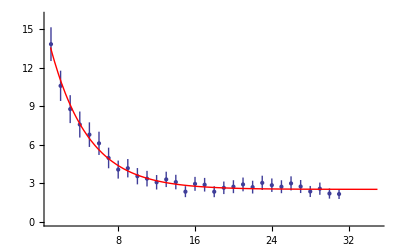

```mathematica
Show[{ErrorBarListPlot[nonlinerr,PlotRange->{0,16}],Plot[nlm[x],{x,-2,35},PlotStyle->Red]}]
```

## On Your Own (70 min)

### (#9) Phase-Shifted Decaying Sinusoid (10 min)

Define an appropriate model and perform a high-quality non-linear least-squares fit of your model against the xy dataset below.  Plot your fitted model and the data on the same graph.  Hint: If you ListPlot the data, it looks a bit like a phase-shifted exponentially-decaying sinusoid.

```mathematica
xydata = {{0.0,5.71855},{0.2,7.29998},{0.4,6.37527},{0.6,2.92445},{0.8,-0.80489},{1.0,-3.97340},{1.2,-5.20427},{1.4,-4.55806},{1.6,-2.16204},{1.8,0.65275},{2.0,2.91818},{2.2,3.67343},{2.4,3.25607},{2.6,1.43566},{2.8,-0.50996},{3.0,-1.94053},{3.2,-2.80186},{3.4,-2.19941},{3.6,-1.30169},{3.8,0.38208},{4.0,1.40752},{4.2,1.90920},{4.4,1.87848},{4.6,0.72315},{4.8,-0.42480},{5.0,-1.11011},{5.2,-1.36038},{5.4,-1.08811},{5.6,-0.66390},{5.8,0.12442},{6.0,0.78261},{6.2,1.17796},{6.4,0.83673},{6.6,0.60683},{6.8,-0.25237},{7.0,-0.63443},{7.2,-0.86788},{7.4,-0.68180},{7.6,-0.23394},{7.8,0.12773},{8.0,0.29089},{8.2,0.45893},{8.4,0.17779},{8.6,0.30576},{8.8,-0.05089},{9.0,-0.15026},{9.2,-0.35048},{9.4,-0.06596},{9.6,-0.22677},{9.8,0.15325},{10.0,0.18327}};
```

### (#10) Checking Mathematica’s Error Estimates (30 min)

Test how good Mathematica’s estimates of fitting parameters are by fitting the model y=k/((e^2-m^2)^2+λ^2) to data generated with this model combined with an additive error having a normal distribution with a mean of 0 and a standard deviation of 0.1.  Use 100 points between 0 and 15 in your data set.  Use the following values for k, m, and λ:

```mathematica
k=100;
m=7;
lambda=8;
```

Repeat this fit 4000 times to get a list of fit values for k, m, and λ.  How do the means and standard deviations of these parameters compare with Mathematica’s estimates?

### (#11) Fitting Variable Star Data (30 min)

The file NGC6811-35.csv is some data digitized from a paper by Michael B. Rose and Eric G. Hintz of BYU entitled “A SEARCH FOR LOW-AMPLITUDE VARIABILITY IN SIX OPEN CLUSTERS USING THE ROBUST MEDIAN STATISTIC” and published in THE ASTRONOMICAL JOURNAL, 134:2067-2078, 2007 November.  It is the magnitude of the star NGC 6811-35 as a function of time. The magnitude of a star is proportional to the log of its brightness.  The first column in the file is the time in hours the star was observed.  The second column is its magnitude.

Assuming the variation in the brightness of the star is sinusoidal, find the brightness of this star as a function of time and then fit the period, amplitude, phase, and average brightness of the star.  Give uncertainties in the three fit parameters.  The amplitude should be positive and the phase should be between 0 and 2 π.  Plot your data and the fit on the same graph to make sure they are reasonable.

```mathematica
Clear["`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Volumes/lyon4/My Documents/School/Semesters/Fall 2011/Physics 230/Lab Notebooks from Teacher

```mathematica
data11 = Import["NGC6811-35.csv"];
{time,size} = Transpose[data11];
```

```mathematica
mynlm =NonlinearModelFit[data11, a*Sin[b*x+c],{a,b,c},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within TraditionalForm`100 iterations.

FittedModel[10.2539 sin(0.000634898 x+1.75887)]

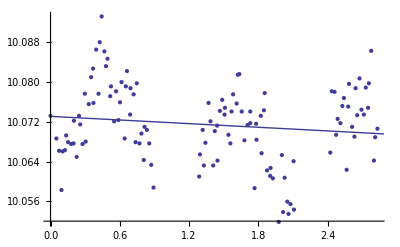

```mathematica
Show[{ListPlot[data11],Plot[mynlm[x],{x,0,3.2}]}]
```